```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\sdeyl\Documents\GitHub\disordered_triangular_swt\calc

```mathematica
fdipole[x_,y_]:=-y/(x^2+y^2)
```

```mathematica
dipole=Table[fdipole[i,j],{i,-20,20},{j,-20,20}];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

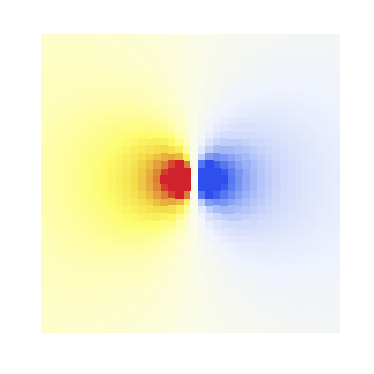

```mathematica
dip=ListDensityPlot[dipole,InterpolationOrder->0,PlotRange-> {-0.25,0.25},ColorFunction->"TemperatureMap",ClippingStyle->ColorData[{"TemperatureMap",{-0.25,0.25}}]/@{-0.25,0.25},Frame-> False]
```

```mathematica
foctupole[x_,y_]:=(y^3-3y x^2)/((x^2+y^2)^3)
```

```mathematica
octupole=Table[foctupole[i,j],{i,-20,20},{j,-20,20}];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

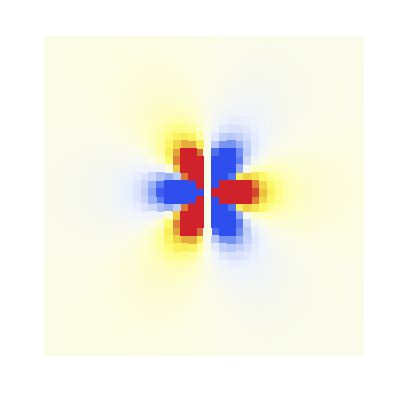

```mathematica
oct=ListDensityPlot[octupole,InterpolationOrder->0,PlotRange-> {-0.005,0.005},ColorFunction->"TemperatureMap",ClippingStyle->ColorData[{"TemperatureMap",{-0.005,0.005}}]/@{-0.005,0.005},Frame-> False]
```

```mathematica
Export["dipole.png",dip]
```

dipole.png

```mathematica
Export["octupole.png",oct]
```

octupole.png